```mathematica
KneserGraph[n_,r_]:=KneserGraph[n,r]=Graph[TwoWayRule@@@Select[Subsets[Subsets[Range[n],{r}],{2}],DisjointQ@@#&]]
```

```mathematica
DistanceKneserGraph[n_,r_]:=Sort[Subgraph[KneserGraph[n,r],#]&/@GroupBy[Subsets[Range[n],{r}],GraphDistance[KneserGraph[n,r],Range[r],#]&]]
```


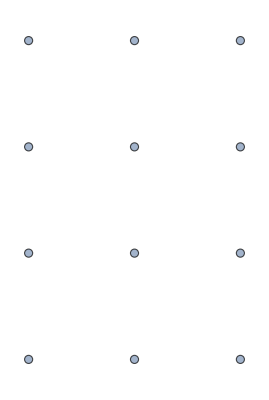
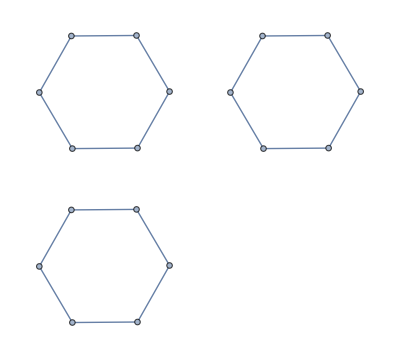
<|0→-Graphics-,1→-Graphics-,2→-Graphics-,3→-Graphics-|>

```mathematica
DistanceKneserGraph[7,3]
```

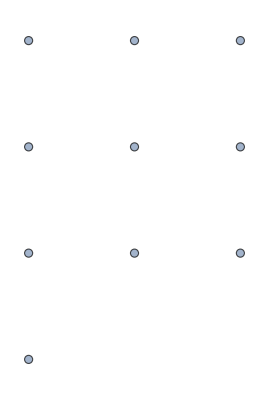
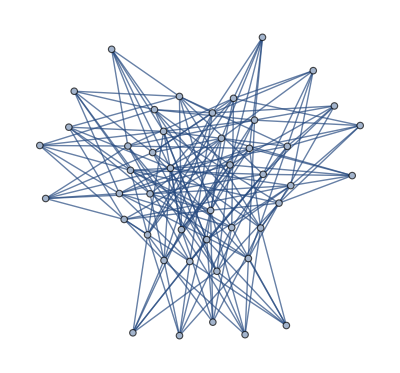
<|0→-Graphics-,1→-Graphics-,2→-Graphics-|>

```mathematica
DistanceKneserGraph[8,3]
```

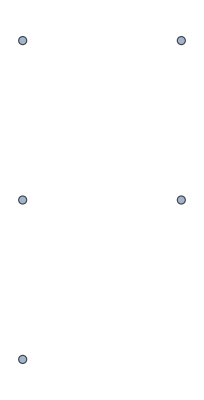
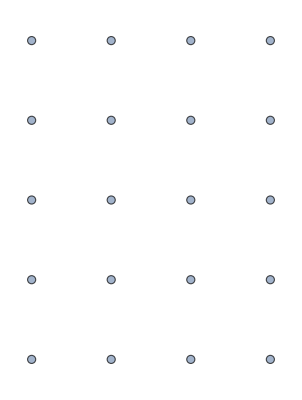
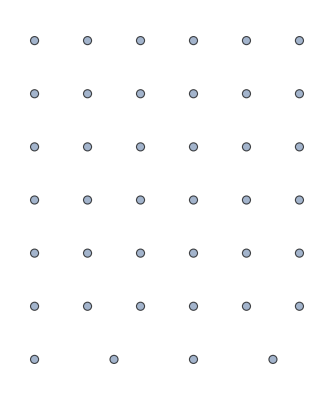
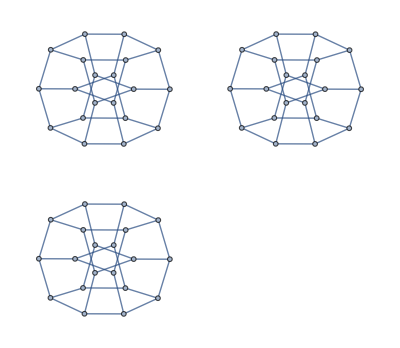
<|0→-Graphics-,1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-|>

```mathematica
DistanceKneserGraph[9,4]
```

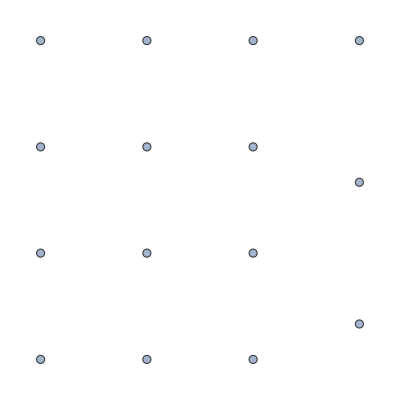
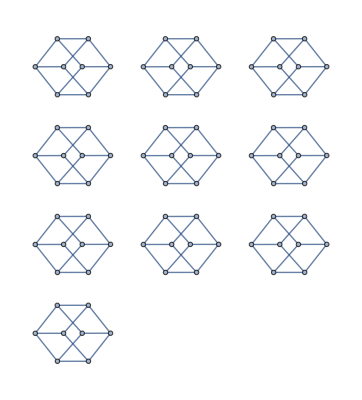
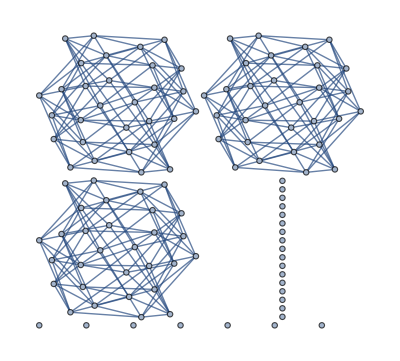
<|0→-Graphics-,1→-Graphics-,3→-Graphics-,2→-Graphics-|>

```mathematica
DistanceKneserGraph[10,4]
```